# nearest neighbor algorithm

## входные данные

### поле:

```mathematica
rows=400;
columns=600;
```

### дроны:

```mathematica
numberOfDrones=5;
turnsOfDrones=5000;
capacityOfDrones = 200;
```

### продукты:

```mathematica
numberOfProducts=5;
productsWeights = RandomInteger[{1,capacityOfDrones},numberOfProducts];
maxNumberOfProductsInWarehouses=300;
```

### склады:

```mathematica
numberOfWarehouses = 3;
```

```mathematica
Clear@generateWarehousesCoords
generateWarehousesCoords[rows_Integer,columns_Integer,number_Integer]:=
Module[
{coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]},

While[ !DuplicateFreeQ[coords],
coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]
];
coords
]
```

```mathematica
warehousesCoords=generateWarehousesCoords[rows,columns,numberOfWarehouses]
```

{{284,246},{477,251},{334,285}}

```mathematica
productsInWarehouses=RandomInteger[maxNumberOfProductsInWarehouses,{numberOfWarehouses,numberOfProducts}]
```

{{24,39,31,59,155},{107,0,16,64,48},{71,31,138,4,14}}

```mathematica
totalNumberOfProducts=Total@productsInWarehouses
```

{202,70,185,127,217}

### заказы:

```mathematica
numberOfOrders =200;
```

```mathematica
Clear@generateOrdersCoords
generateOrdersCoords[rows_Integer,columns_Integer,number_Integer,warehouses:{{_Integer,_Integer}..}]:=
Module[
{coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]},

While[ !DuplicateFreeQ[coords~Join~warehousesCoords],
coords=Thread[{RandomInteger[columns,number],RandomInteger[rows,number]}]
];
coords
]
```

```mathematica
ordersCoords=generateOrdersCoords[rows,columns,numberOfOrders,warehousesCoords];
```

```mathematica
Floor[Mean@totalNumberOfProducts/numberOfOrders]
```

0

```mathematica
Clear@generateOrders
generateOrders[numberOfOrders_Integer,totalNumberOfProducts_List]:=
({1}~Join~ConstantArray[0,numberOfProducts-1])+#&/@RandomInteger[
Min[Floor[Mean@totalNumberOfProducts/numberOfOrders],3],
{numberOfOrders,Length@totalNumberOfProducts}
]
```

```mathematica
orders=generateOrders[numberOfOrders,totalNumberOfProducts];
```

### база данных:

```mathematica
data=<|
"general"-> <|
"rows"->rows,
"columns"->columns,
"turns"-> turnsOfDrones,
"capacity"-> capacityOfDrones,
"numberOfDrones"->numberOfDrones,
"numberOfProducts"->numberOfProducts,
"numberOfWarehouses"-> numberOfWarehouses,
"numberOfOrders"-> numberOfOrders,
"weightsOfProducts"->productsWeights
|>,

"drones"->AssociationThread[Range@numberOfDrones->(<|"coords"->#⟦1⟧,"products"->#⟦2⟧,"score"->#⟦3⟧,"order"->-1|>&/@Thread[{ConstantArray[warehousesCoords⟦1⟧,numberOfDrones],ConstantArray[0,{numberOfDrones,numberOfProducts}],ConstantArray[0,numberOfDrones]}])],

"warehouses"->AssociationThread[Range@numberOfWarehouses->(<|"coords"->#⟦1⟧,"products"->#⟦2⟧|>&/@Thread[{warehousesCoords,productsInWarehouses}])],

"orders"-><|
"order"->AssociationThread[Range@numberOfOrders->(<|"coords"->#⟦1⟧,"list"->#⟦2⟧,"turns"-> 0|>&/@Thread[{ordersCoords,orders}])],
"mask"->ConstantArray[0,numberOfOrders]
|>
|>;
```

```mathematica
data;
```

## анализ данных

```mathematica
plot=ListPlot[{MapThread[Labeled,{Values@data⟦"warehouses",All,"coords"⟧,Range@data["general","numberOfWarehouses"]}],MapThread[Labeled,{Values@data⟦"orders","order",All,"coords"⟧,
Range@data["general","numberOfOrders"]}]},PlotTheme->"Detailed",PlotStyle->{PointSize[0.03],PointSize[0.02]}];
```

## алгоритм

на каждой итерации параллельно посылаем дронов на заказы (несколько дронов могут выбрать один заказ и закрыть его за один ход), при этом бронируя продукты.

```mathematica
plot;
```

```mathematica
Clear@loadProducts
loadProducts[data_Association,warehouseID_Integer,orderID_Integer,droneID_Integer]:=
Module[
{tempData=data,capacity =data["general","capacity"],weights=data["general","weightsOfProducts"],numberOfProduct},
Do[
numberOfProduct=
Min[
data⟦"warehouses",warehouseID,"products",i⟧,
data⟦"orders","order",orderID,"list",i⟧,
Quotient[capacity,weights⟦i⟧]
];
tempData⟦"warehouses",warehouseID,"products",i⟧-=numberOfProduct;
tempData⟦"drones",droneID,"products",i⟧+=numberOfProduct;
capacity-=weights⟦i⟧ numberOfProduct;

(*If[numberOfProduct>0,
Print["дрон ",droneID," загрузил ",numberOfProduct, " у.е. продукта ", i, " со склада ",warehouseID," для заказа ", orderID]];*)

If[capacity≤0,
Break[]
]

,{i,Length@weights}];
tempData
]
```

```mathematica
Clear@calculateTurns
calculateTurns[turn_Integer,data_Association]:=
With[{T=data["general","turns"]},Ceiling[(T-turn)/T 100]]
```

```mathematica
Clear@unloadProduct
unloadProduct[data_Association,orderID_Integer,droneID_Integer]:=
Module[
{tempData=data},
tempData⟦"orders","order",orderID,"list"⟧-=tempData⟦"drones",droneID,"products"⟧;
tempData⟦"drones",droneID,"products"⟧=ConstantArray[0,data["general","numberOfProducts"]];

If[Total@tempData⟦"orders","order",orderID,"list"⟧==0,
tempData⟦"orders","mask",orderID⟧=1;
tempData["orders","order",orderID,"turns"]=calculateTurns[tempData["drones",droneID,"score"],tempData]
(*Print["заказ ",orderID, " полностью выполнен"]*)
];
tempData
]
```

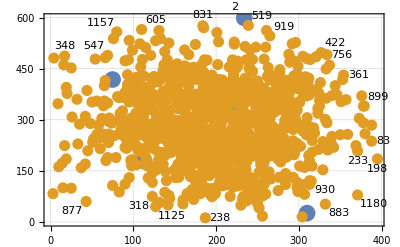

```mathematica
plot
```

```mathematica
Clear@chooseNextDirection
chooseNextDirection[droneID_,data_Association]:=
Module[
{warehouses,warehouse,order={},warehouseCoords,orderID,orderCoords,tempData=data},

If[
Total@data["orders","mask"]≠data["general","numberOfOrders"],
(*выбор ближайшего склада, где есть хотя бы один продукт*)
warehouses=SortBy[
Normal@
Select[
data⟦"warehouses"⟧,
Total@#["products"]≠0&
]⟦All,"coords"⟧,
Ceiling@EuclideanDistance[Last@#,data["drones",droneID,"coords"]]&];

If[warehouses=={},Print["ass"]];
(*определяем ближайший заказ*)
Do[
order=First[
SortBy[
Normal@Select[
Pick[data⟦"orders","order",All⟧,data["orders","mask"],0],Composition[Greater[#,0]&,Total,Times[tempData["warehouses",warehouseLocal⟦1⟧,"products"],#["list"]]&]
]⟦All,"coords"⟧
,
Ceiling@EuclideanDistance[warehouseLocal⟦2⟧,Last@#]&],
{}];
If[order=!={},
warehouse=warehouseLocal;
Break[]],
{warehouseLocal,warehouses}];

warehouseCoords=warehouse⟦2⟧;
orderID=order⟦1⟧;
orderCoords=order⟦2⟧;

(*"бронируем" продукты, то есть сразу же загружаем*)

tempData=loadProducts[tempData,warehouse⟦1⟧,orderID,droneID];

tempData["drones",droneID,"coords"]=orderCoords;
tempData["drones",droneID,"order"]=orderID;
tempData["drones",droneID,"score"]=Ceiling@EuclideanDistance[data["drones",droneID,"coords"],warehouseCoords]+Ceiling@EuclideanDistance[warehouseCoords,orderCoords];
If[
tempData["drones",droneID,"score"]>data["general","turns"],
Print["превышено количество ходов"];
Abort[]
];

(*разгружаем*)
unloadProduct[tempData,orderID,droneID],
tempData
]
]
```

```mathematica
Clear@solve
solve[data_Association]:=
Module[
{tempData=data},
If[!And@@Positive[Total@Values@data⟦"warehouses",All,"products"⟧-Total@Values@data⟦"orders","order",All,"list"⟧],
Print["недостаточно продуктов на складах"];Return[{}]
];
While[
Total@tempData["orders","mask"]≠data["general","numberOfOrders"],
Do[
tempData=chooseNextDirection[i,tempData]
,{i,tempData["general","numberOfDrones"]}
]
];
tempData
]
```

```mathematica
solution=solve[data];
```

заказ 391 полностью выполнен

заказ 410 полностью выполнен

заказ 662 полностью выполнен

заказ 32 полностью выполнен

заказ 1117 полностью выполнен

заказ 1005 полностью выполнен

заказ 393 полностью выполнен

заказ 804 полностью выполнен

заказ 206 полностью выполнен

заказ 373 полностью выполнен

заказ 1023 полностью выполнен

заказ 543 полностью выполнен

заказ 637 полностью выполнен

заказ 717 полностью выполнен

заказ 805 полностью выполнен

заказ 132 полностью выполнен

заказ 920 полностью выполнен

заказ 854 полностью выполнен

заказ 276 полностью выполнен

заказ 664 полностью выполнен

заказ 294 полностью выполнен

заказ 882 полностью выполнен

заказ 426 полностью выполнен

заказ 679 полностью выполнен

заказ 195 полностью выполнен

заказ 595 полностью выполнен

заказ 1188 полностью выполнен

заказ 277 полностью выполнен

заказ 1155 полностью выполнен

заказ 665 полностью выполнен

$Aborted

```mathematica
And@@Positive[Total@Values@data⟦"warehouses",All,"products"⟧-Total@Values@data⟦"orders","order",All,"list"⟧]
```

True

```mathematica
Total@Values@data⟦"orders","order",All,"list"⟧==(Total@Values@data⟦"warehouses",All,"products"⟧-Total@Values@solution⟦"warehouses",All,"products"⟧)
```

True

```mathematica
Total@Values@data⟦"orders","order",All,"list"⟧
```

{200,0,0,0,0}

```mathematica
Values@solution⟦"warehouses",All,"products"⟧
```

{{0,39,31,59,155},{2,0,16,64,48},{0,31,138,4,14}}

```mathematica
SortBy[solution⟦"orders","order",All,"turns"⟧,Value]
```

<|80→81,129→81,180→81,189→81,31→82,67→82,83→82,95→82,122→82,130→82,131→82,155→82,159→82,168→82,48→83,69→83,74→83,123→83,185→83,22→84,47→84,59→84,71→84,76→84,196→84,72→85,55→86,133→88,9→89,34→89,96→89,134→89,165→89,7→90,19→90,29→90,33→90,35→90,49→90,53→90,63→90,68→90,89→90,94→90,101→90,114→90,115→90,128→90,195→90,10→91,60→91,93→91,97→91,99→91,109→91,135→91,137→91,158→91,160→91,163→91,172→91,174→91,176→91,178→91,184→91,187→91,193→91,199→91,3→92,21→92,26→92,64→92,65→92,103→92,119→92,132→92,139→92,142→92,170→92,62→93,79→93,100→93,106→93,111→93,141→93,145→93,148→93,167→93,186→93,6→94,12→94,32→94,44→94,51→94,61→94,73→94,81→94,86→94,98→94,102→94,143→94,153→94,161→94,182→94,200→94,1→95,5→95,8→95,15→95,24→95,28→95,75→95,84→95,87→95,117→95,140→95,149→95,154→95,166→95,175→95,179→95,188→95,2→96,16→96,20→96,25→96,39→96,45→96,46→96,50→96,70→96,77→96,82→96,85→96,105→96,107→96,121→96,152→96,173→96,181→96,183→96,191→96,192→96,198→96,4→97,17→97,18→97,23→97,36→97,38→97,40→97,42→97,57→97,58→97,92→97,108→97,110→97,112→97,124→97,125→97,126→97,127→97,156→97,162→97,164→97,169→97,171→97,190→97,27→98,30→98,37→98,52→98,54→98,88→98,90→98,104→98,120→98,138→98,147→98,151→98,157→98,194→98,11→99,14→99,78→99,91→99,113→99,116→99,118→99,144→99,146→99,177→99,13→100,41→100,43→100,56→100,66→100,136→100,150→100,197→100|>